## Problem 9-7

```mathematica
hbar=1.055 10^-34;
m=9.11 10^-31;
ρ=2 10^-11;
σ=1/ρ;
Z=1;
a=4.3 10^-10;
n=(2 Z)/a^3;
e=1.602 10^-19;
Ef=hbar^2/(2 m)(3 π^2 n)^(2/3);
v=√((2 Ef)/m);
tau=(σ m)/(n e^2);
v tau
```

0.0000740664

## Problem 9-8

Effective mass will be positive from 0 to about 0.5 Å^-1, then infinite at that point, then negative from then until around 1.2Å, then infinite at that point and then negative until 1.25Å.

## Problem 9-9

375074. √(Sin[k/4000000000]^2)

375074.

0

(1.38954×10^-30)/(Cos[k/4000000000]^2-1. Sin[k/4000000000]^2)

8.67381×10^-12

-8.67381×10^-12

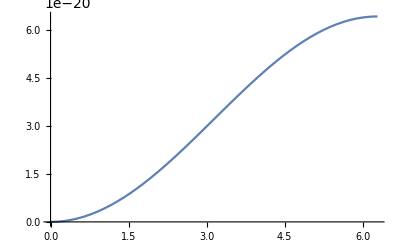

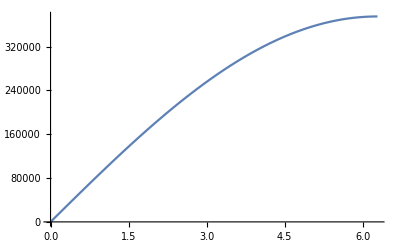

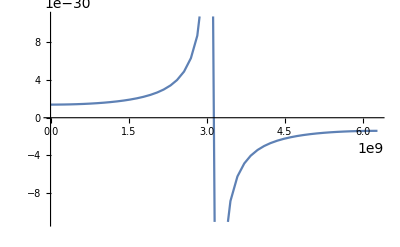

```mathematica
(* Part A *)
γ=0.1 e;
a=5 10^-10;
En=4γ Sin[(k a)/2]^2;
v=√((2En)/m)
vmax=√((2 4 γ)/m)
vmin = 0
(* Part B *)
mstar=(1/hbar^2 D[En,{k,2}])^-1//Simplify
mstar0=(mstar/.k->0)/e
mstarPiOvA=(mstar/.k->π/a)/e
(* Part C *)
Plot[En,{k,0,π/a}]
Plot[v,{k,0,π/a}]
Plot[mstar,{k,0,π/a}]
```

## Problem 9-10

```mathematica
Clear[m];
En=a1(kx+ky)^2+a2(kx-ky)^2+a3 kz^2;
v=√((2 En)/m)
EffMTens={{1/hbar^2 D[En,{kx,2}], 1/hbar^2 D[En,{kx,1},{ky,1}], 1/hbar^2 D[En,{kx,1},{kz,1}]}, {1/hbar^2 D[En,{kx,1},{ky,1}], 1/hbar^2 D[En,{kx,2}], 1/hbar^2 D[En,{kz,1},{ky,1}]}, {1/hbar^2 D[En,{kx,1},{kz,1}], 1/hbar^2 D[En,{kz,1},{ky,1}], 1/hbar^2 D[En,{kx,2}]}};
MatrixForm[EffMTens]
```

√2 √((a2 (kx-ky)^2+a1 (kx+ky)^2+a3 kz^2)/m)

(8.98452×10^67 (2 a1+2 a2) | 8.98452×10^67 (2 a1-2 a2) | 0.
8.98452×10^67 (2 a1-2 a2) | 8.98452×10^67 (2 a1+2 a2) | 0.
0. | 0. | 8.98452×10^67 (2 a1+2 a2))